```mathematica
Fisheries management

In this Figure we plot the profit for the ecologically enlightened and for the evolutionary enlightened manager. For details about the calculation of the Nash and Stackelberg strategies and outcomes, see Salvioli,M; Dubbeldam,J; Staňková,K; Brown J.S.(2021). Fisheries management as a Stackelberg Evolutionary Game: Finding an evolutionarily enlightened strategy.Plos one,16(1) ,e0245255.
```

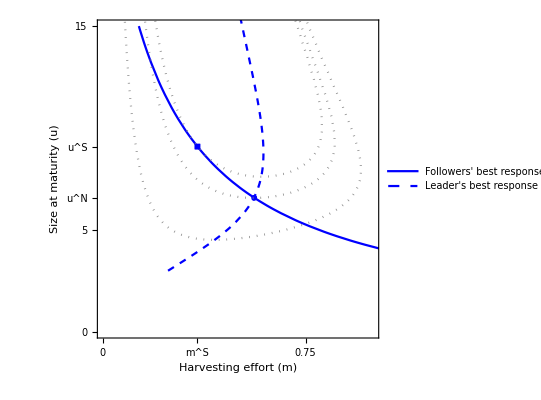

```mathematica
ClearAll;
SetOptions[Plot,BaseStyle->{FontFamily->"CMU Sans Serif",FontSize->18}];

s=1;
g=5;
R=4;
d=0.2;
z=3;
c=5;

m^N=0.56;
m^S=0.35;

(*The coordinates and outcomes of the Nash and Stackelberg equilibria are (m^N=0.56,u^N=6.58,Q^N=2.24) 
and (m^S=0.35,u^S=9.09,Q^S=2.76)  *)

ProfitFunction[s_,u_,R_,m_,z_,g_,d_,c_]:=(m*R)/(u*(m+d))*Log[(s*u*Exp[(-m*(u-z))/g]*Exp[(-d*u)/g])/(m+d)]*(((m+d)*z+g)/(Exp[(-m*(u-z))/g]*Exp[(-d*u)/g]*Exp[(d*z)/g])-g)-(c*m);


FollowerBR=Plot[Piecewise[{{g/(m+d),(g/(m+d))>=z},{Min[g/d,z],(g/(m+d))<z}}],{m,0,5},PlotRange->{{0,1},{0,15}},PlotStyle->{Blue,Thick},AspectRatio->1,PlotLegends->{"Followers' best response"}];

LeaderBR=ParametricPlot[{m/.First[Last[NMaximize[{ProfitFunction[s,u,R,m,z,g,d,c],0≤m≤ 2.5 },m]]],u},{u,z,70},PlotRange->{{0,1},{0,15}},PlotStyle->{Blue,Dashed},AspectRatio->1,PlotLegends->{"Leader's best response"}];


Stackelberg=ListPlot[{{m^S,g/(m^S+d)}},PlotMarkers->{{■,15}},PlotStyle->{Blue}];

Nash=ListPlot[{{m^N,g/(m^N+d)}},PlotMarkers->{{●,14}},PlotStyle->{Blue}];

LevelCurves=ContourPlot[{ProfitFunction[s,u,R,m,z,g,d,c]==2.76147,ProfitFunction[s,u,R,m,z,g,d,c]==2.24485,ProfitFunction[s,u,R,m,z,g,d,c]==1.2},{m,0,1},{u,2,20},ContourStyle->{{Gray,Dotted},{Gray,Dotted}}];

Show[{FollowerBR,LeaderBR,Stackelberg,Nash,LevelCurves},Frame->{{True,False},{True,False}},FrameLabel->{{"Size at maturity (u)",None},{"Harvesting effort (m)",None}},FrameTicks->{{{0,5,{6.58,"u^N"},{9.09,"u^S"},15},None},{{0,0.25,{0.350012,"m^S"},{0.56,"m^N"},0.75,1},None}}, FrameTicksStyle->Directive[Black],LabelStyle->Directive[Black,18]]
```